# Assignment 3, Part 3

```mathematica
SetDirectory["C:\\Users\\brook\\Documents\\Workspaces\\CSC 450\\CSC450\\assignment3"]
FileNames[]
```

C:\Users\brook\Documents\Workspaces\CSC 450\CSC450\assignment3

{a3_notebook2.nb,a3_notebook3.nb,a3_notebook.nb,a3_p1_f1_1D.csv,a3_p1_f1.csv,a3_p1_f1_ground.csv,a3_p1_f2_1D.csv,a3_p1_f2.csv,a3_p1_f2_ground.csv,a3_p1_f3.csv,a3_p1_f4.csv,a3_p1_f5_1D.csv,a3_p1_f5.csv,a3_p1_f5_ground.csv,a3_p1_f6.csv,Mathematica.md,meta camera changes.json,meta main.json,output1_b.csv,output3_f10.csv,output3_f11.csv,output3_f12.csv,output3_f6.csv,output3_f7.csv,output3_f8.csv,output3_f9.csv,output3_p4_1_1_1.csv,output3_p4_1_1_2.csv,output3_p4_1_1_3.csv,output3_p4_1_1_4.csv,output3_p4_1_1_5.csv,output3_p4_1_2a_1.csv,output3_p4_1_2a_2.csv,output3_p4_1_2a_3.csv,output3_p4_1_2a_4.csv,output3_p4_1_2a_5.csv,output3_p4_1_2b_1.csv,output3_p4_1_2b_2.csv,output3_p4_1_2b_3.csv,output3_p4_1_2b_4.csv,output3_p4_1_2b_5.csv,output3_p4_a.csv,output3_p4_b.csv,output3_p4_c.csv,output3_p4_d.csv,output3_p4_e.csv,output3_p4_f.csv,output3_p4_g.csv}

## Partial Registration

## Visualization

```mathematica
(*Import the CSV file*)
data=Import["output3_p4_a.csv","CSV"];

(*Define the function f, the point m, and the norm 1 function*)
f[x_]:=x^2*Sin[x];
m={1,-3};
norm1[p_,q_]:=Abs[p[[1]]-q[[1]]]+Abs[p[[2]]-q[[2]]];

(*Define the function for the boundary of the norm-1, a diamond shape*)
diamond[x_,y_]:=norm1[m,{x,y}]-1;

(*Create the animation*)
frames=Table[ContourPlot[{f[x]==y,diamond[x,y]==0},{x,-3,4},{y,-8,8},Epilog->{Red,PointSize[Large],Point[m],Blue,PointSize[Medium],Point[{data[[i,1]],f[data[[i,1]]]}],Dashed,Line[{m,{data[[i,1]],f[data[[i,1]]]}}]}],{i,Length[data]}];
ListAnimate[frames]
```

## Examples

```mathematica
(*Define the function for plotting*)
plotFandNorm[f_,m_,xMin_,xMax_,yMin_,yMax_,normType_,filename_]:=Module[{data,plotF,plotM,plotNorm,plotClosestPoint,lines,norm},
(*Import the data*)
data=Import[filename,"CSV"];
(*Define the norm based on the normType argument; 1 is for norm1, 2 for norm2, 3 for norm infinity*)
norm=Switch[normType,
1,Abs[#1[[1]]-#2[[1]]]+Abs[#1[[2]]-#2[[2]]]&,
2,Sqrt[(#1[[1]]-#2[[1]])^2+(#1[[2]]-#2[[2]])^2]&,
3,Max[Abs[#1[[1]]-#2[[1]]],Abs[#1[[2]]-#2[[2]]]]&];

(*Create the plots*)
plotF=Plot[f[x],{x,xMin,xMax},PlotStyle->Blue];
plotM=ListPlot[{m},PlotStyle->{Red,PointSize[0.02]}];
plotNorm=RegionPlot[norm[m,{x,y}]<=1,{x,xMin,xMax},{y,yMin,yMax},PlotStyle->Directive[Green,Opacity[0.3]],BoundaryStyle->Green];
plotClosestPoint=ListPlot[{data[[-1,1;;2]]},PlotStyle->{Green,PointSize[0.02]}];

(*Create the dashed line between the point m and the determined closest point*)
lines=Graphics[{Dashed,Line[{m,data[[-1,1;;2]]}]}];

(*Show all plots*)
Show[plotNorm,plotF,plotM,plotClosestPoint,lines]]
```

The  following  examples  show  norm  1, norm  2, and  norm  infinity  plotting  with  the  function  x^2 * sin (x)  over  the  range  of [-1, 2]  with  m  defined  at  (-1, 3) .

### Example 1

Norm 1

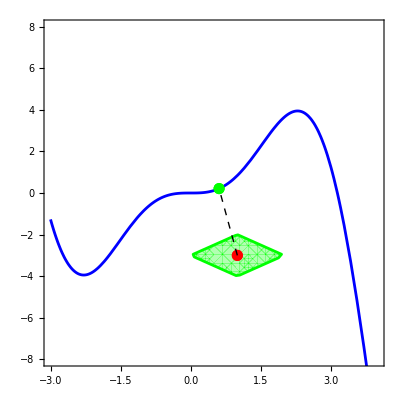

```mathematica
f4a[x_]:=x^2*Sin[x];
m1={1,-3};
(* Pass in the function, the point, the borders for X and Y, and the input CSV name *)
plotFandNorm[f4a,m1,-3,4,-8,8,1,"output3_p4_b.csv"]
```

### Example 2

Norm 2

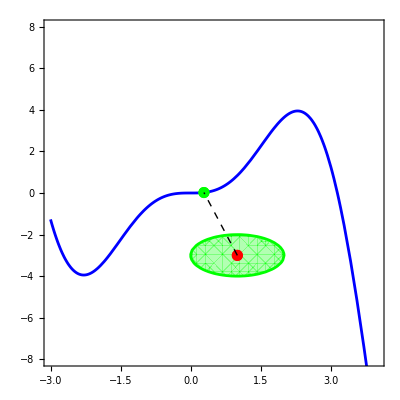

```mathematica
plotFandNorm[f4a,m1,-3,4,-8,8,2,"output3_p4_c.csv"]
```

### Example 3

Norm infinity

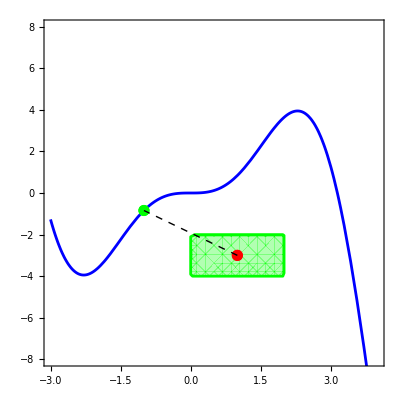

```mathematica
plotFandNorm[f4a,m1,-3,4,-8,8,3,"output3_p4_d.csv"]
```

### Example 4

This next example has a different function where I mixed up the points to choose ones above and below the oscillations.

There’s 3 m points, each using a different norm and set with different ranges on the X to test where it finds the minimum.

```mathematica
f4b[x_] = x-8Sin[x]*Cos[2x];
```

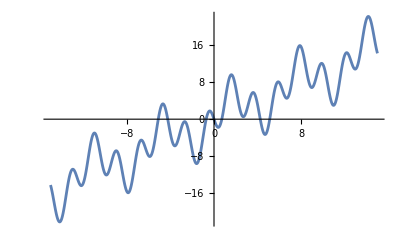

```mathematica
Plot[f4b[x],{x,-15, 15}]
```

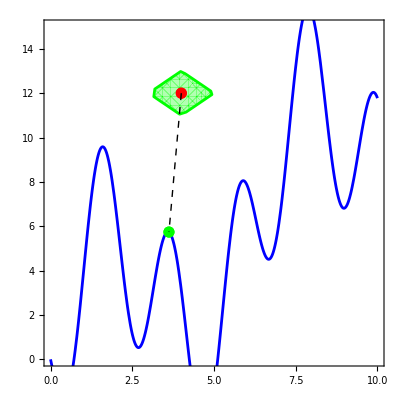

```mathematica
m2a={4,12};
plotFandNorm[f4b,m2a,-0,10,0,15,1,"output3_p4_e.csv"]
```

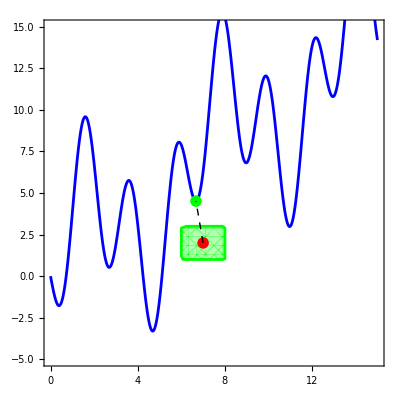

```mathematica
m2c={7,2};
plotFandNorm[f4b,m2c,0,15,-5,15,3,"output3_p4_g.csv"]
```

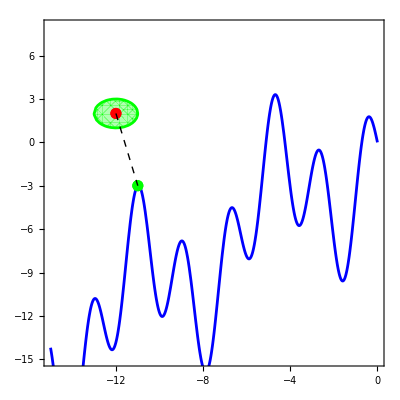

```mathematica
m2b={-12,2};
plotFandNorm[f4b,m2b,-15,0,-15,8,2,"output3_p4_f.csv"]
```

## Fitting From Multiple Points

The function we’re working with

```mathematica
f5[x_]=x^2*Sin[x]
```

x^2 Sin[x]

```mathematica
x^2 Sin[x]
```

x^2 Sin[x]

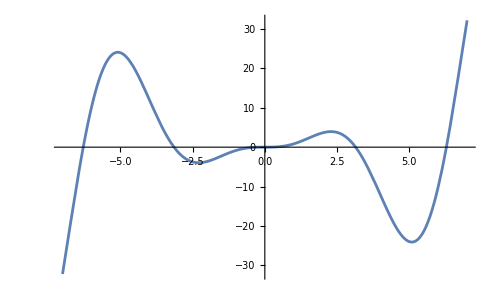

```mathematica
Plot[x^2 Sin[x],{x,-7,7}]
```

Define a new function that’s a modified version of the one above that takes the 5 closest points’ CSVs, the function itself, and defines the 3 norm function boundaries.

```mathematica
plotFandNorm[f_,m_,xMin_,xMax_,yMin_,yMax_,normType_,filename_]:=Module[{data,plotF,plotM,plotNorm,plotClosestPoint,lines,norm,plots={}},
(*Define the norm based on the normType argument; 1 is for norm1,2 for norm2,3 for norm infinity*)
norm=Switch[normType,1,Abs[#1[[1]]-#2[[1]]]+Abs[#1[[2]]-#2[[2]]]&,2,Sqrt[(#1[[1]]-#2[[1]])^2+(#1[[2]]-#2[[2]])^2]&,3,Max[Abs[#1[[1]]-#2[[1]]],Abs[#1[[2]]-#2[[2]]]]&];
(*Create the plots*)
plotF=Plot[f[x],{x,xMin,xMax},PlotStyle->Blue];
For[i=1,i<=Length[m],i++,
(*Import the data*)
data=Import[filename[[i]],"CSV"];
plotM=ListPlot[{m[[i]]},PlotStyle->{Red,PointSize[0.02]}];
plotNorm=RegionPlot[norm[m[[i]],{x,y}]<=1,{x,xMin,xMax},{y,yMin,yMax},PlotStyle->Directive[Green,Opacity[0.3]],BoundaryStyle->Green];
plotClosestPoint=ListPlot[{data[[-1,1;;2]]},PlotStyle->{Green,PointSize[0.02]}];
(*Create the dashed line between the point m and the determined closest point*)
lines=Graphics[{Dashed,Line[{m[[i]],data[[-1,1;;2]]}]}];
(*Add the plots to the list of plots*)
AppendTo[plots,Show[plotNorm,plotF,plotM,plotClosestPoint,lines]];];
(*Show all plots*)
plots]
```

### Example

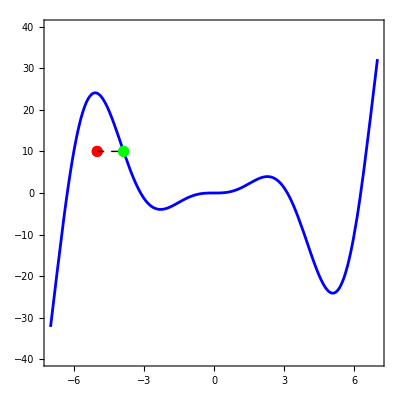
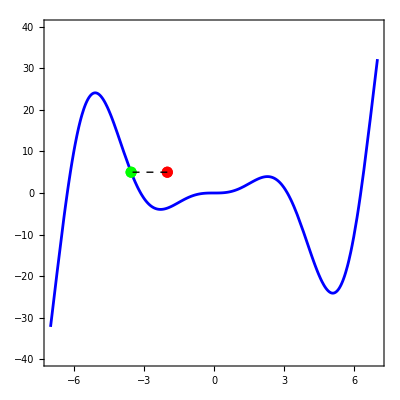
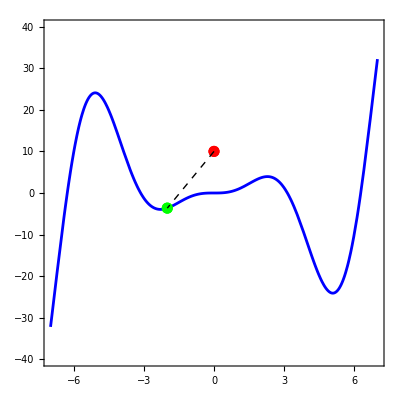
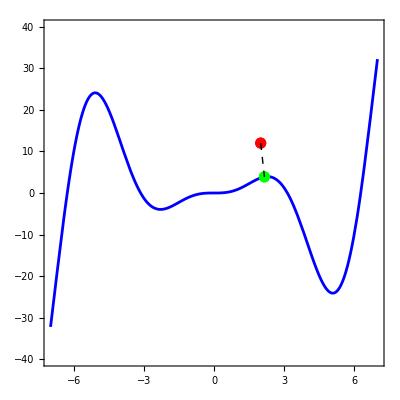
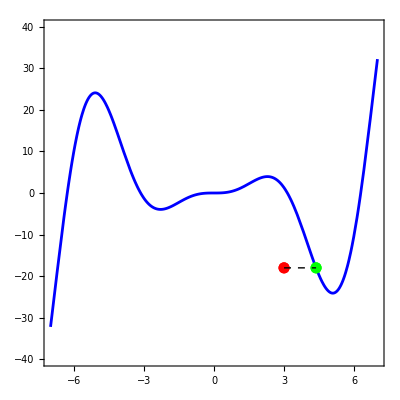

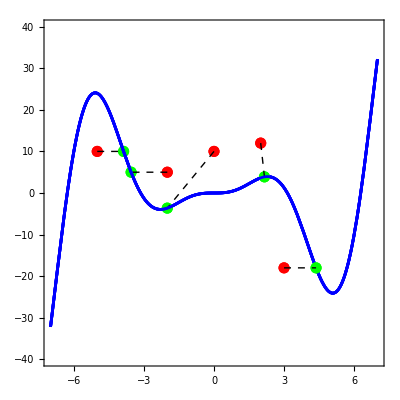

```mathematica
f[x_]:=x^2*Sin[x]

(*Define the points m*)
m={{-5,10},{-2,5},{0,10},{2,12},{3,-18}};

(*Define the range of x and y values for the plot*)
xMin=-7;
xMax=7;
yMin=-40;
yMax=40;

(*Define the norm types for each point*)
normType={1,1, 1, 1, 1, 1};

(*Define the filenames for the CSV files*)
filename={"output3_p4_1_1_1.csv","output3_p4_1_1_2.csv","output3_p4_1_1_3.csv","output3_p4_1_1_4.csv","output3_p4_1_1_5.csv"};

(*Call the function*)
plots=plotFandNorm[f,m,xMin,xMax,yMin,yMax,normType,filename]

(*Display the plots*)
Show[plots]
```

Red still represents the initial point, and green is the destination point.

### Plotting the Optimized Function

This function is again an improved version of the previous one that now graphs the newly optimized function to minimize the distance between all the points
along with the old function and points.

```mathematica
plotOptimizedF[f_,a_,m_,xMin_,xMax_,yMin_,yMax_,normType_,filename_]:=Module[{data,plotF,plotFa,plotM,plotNorm,plotClosestPoint,lines,norm,plots={}},(*Define the norm based on the normType argument;1 is for norm1,2 for norm2,3 for norm infinity*)
norm=Switch[normType,1,Abs[#1[[1]]-#2[[1]]]+Abs[#1[[2]]-#2[[2]]]&,2,Sqrt[(#1[[1]]-#2[[1]])^2+(#1[[2]]-#2[[2]])^2]&,3,Max[Abs[#1[[1]]-#2[[1]]],Abs[#1[[2]]-#2[[2]]]]&];
(*Create the plots*)
plotF=Plot[f[x],{x,xMin,xMax},PlotStyle->Blue];
plotFa=Plot[f[x]+a,{x,xMin,xMax},PlotStyle->Purple];
For[i=1,i<=Length[m],i++,
(*Import the data*)
data=Import[filename[[i]],"CSV"];
plotM=ListPlot[{m[[i]]},PlotStyle->{Red,PointSize[0.02]}];
plotNorm=RegionPlot[norm[m[[i]],{x,y}]<=1,{x,xMin,xMax},{y,yMin,yMax},PlotStyle->Directive[Green,Opacity[0.3]],BoundaryStyle->Green];
plotClosestPoint=ListPlot[{data[[-1,1;;2]]},PlotStyle->{Green,PointSize[0.02]}];
(*Create the dashed line between the point m and the determined closest point*)
lines=Graphics[{Dashed,Line[{m[[i]],data[[-1,1;;2]]}]}];
(*Add the plots to the list of plots*)
AppendTo[plots,Show[plotNorm,plotF,plotFa,plotM,plotClosestPoint,lines]];];
(*Show all plots*)
plots]
```

#### Norm 1

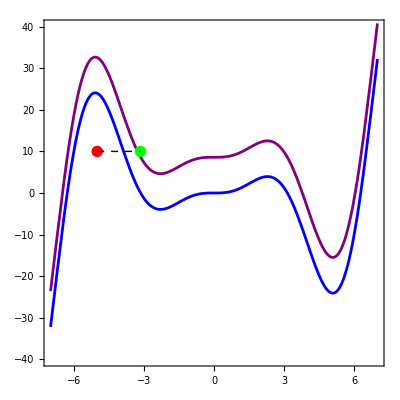
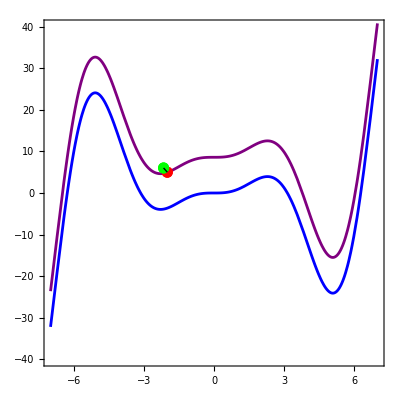
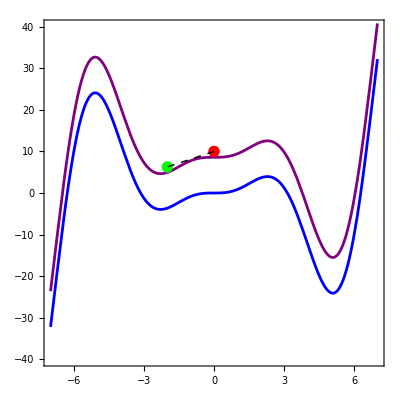
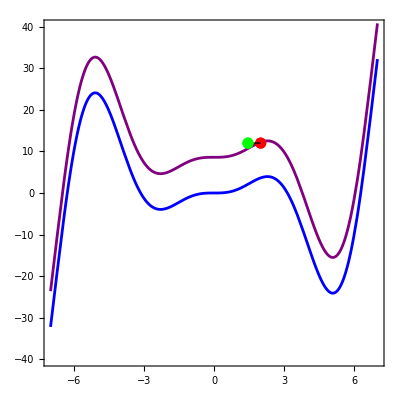
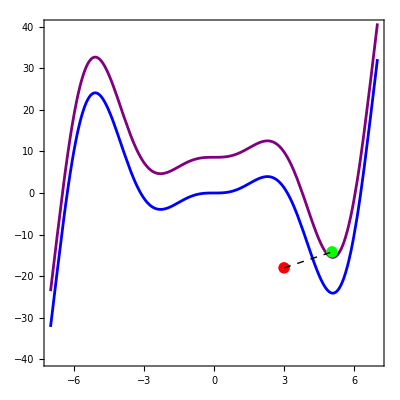

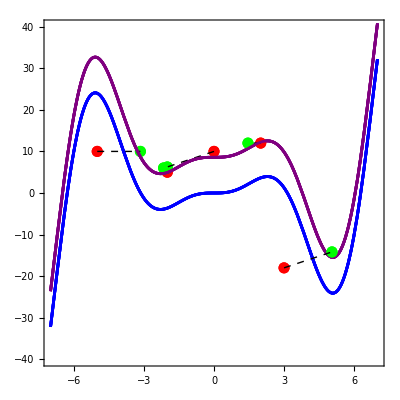

```mathematica
f[x_]:=x^2*Sin[x]

(*Define the points m*)
m={{-5,10},{-2,5},{0,10},{2,12},{3,-18}};

(*Define the range of x and y values for the plot*)
xMin=-7;
xMax=7;
yMin=-40;
yMax=40;

(*Define the norm types for each point*)
normType={1,1, 1, 1, 1, 1};

(*Define the filenames for the CSV files*)
filename={"output3_p4_1_2a_1.csv","output3_p4_1_2a_2.csv","output3_p4_1_2a_3.csv","output3_p4_1_2a_4.csv","output3_p4_1_2a_5.csv"};

(*Call the function*)
plots=plotOptimizedF[f,8.59,m,xMin,xMax,yMin,yMax,normType,filename]

(*Display the plots*)
Show[plots]
```

This is officially the coolest part of any assignment we’ve done all semester!
As we can see the blue function is the old function f (x) = x^2 * sin(x) and the purple line is the new, optimized function fa(x) = x^2 * sin(x) + a, where a = 8.599.
Produced a score of 10.552 at a = 8.599.

#### Norm 2

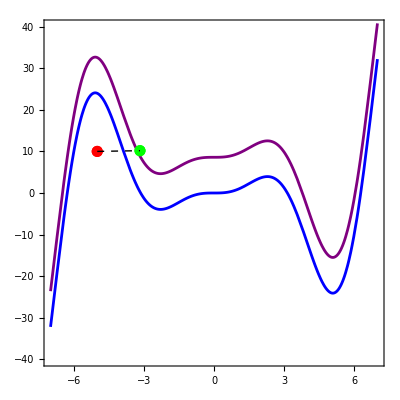
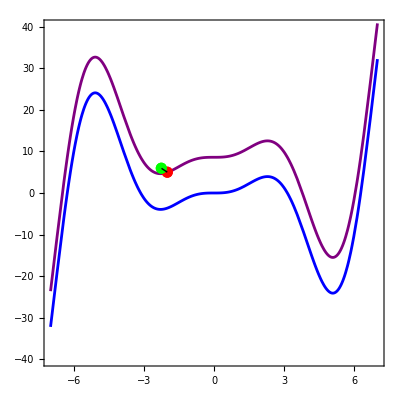
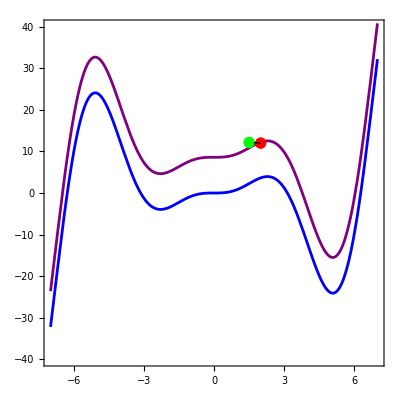
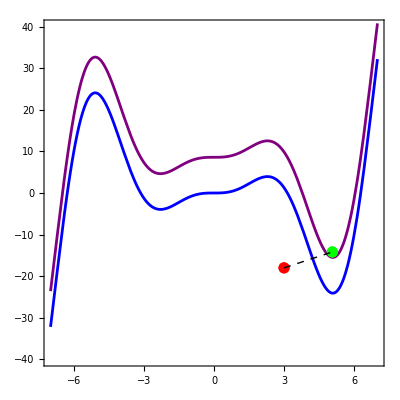
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

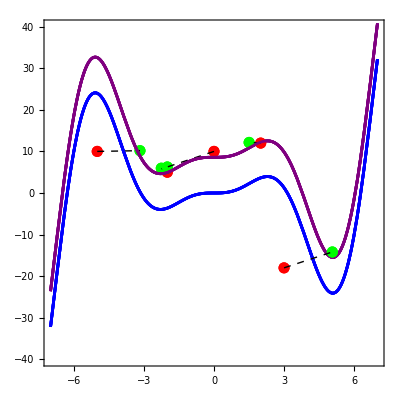

```mathematica
(*Define the norm types for each point*)
normType={2,2, 2, 2, 2, 2};

(*Define the filenames for the CSV files*)
filename={"output3_p4_1_2b_1.csv","output3_p4_1_2b_2.csv","output3_p4_1_2b_3.csv","output3_p4_1_2b_4.csv","output3_p4_1_2b_5.csv"};

(*Call the function*)
plots=plotOptimizedF[f,8.59,m,xMin,xMax,yMin,yMax,normType,filename]

(*Display the plots*)
Show[plots]
```

Produced a score of 6.401 from an a = 9.400

#### Norm Infinity

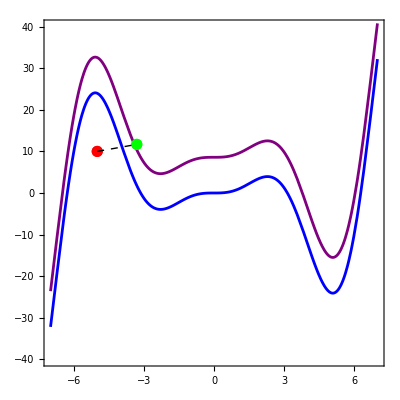
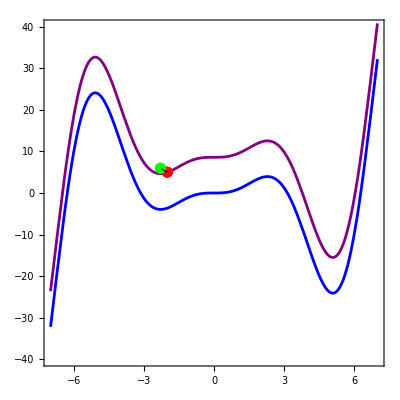
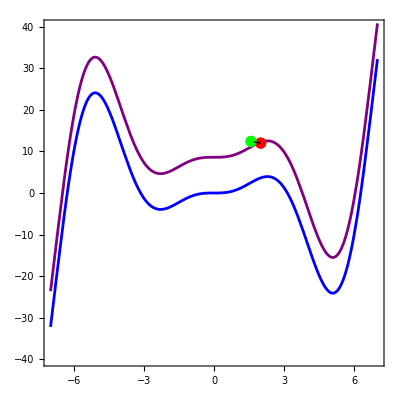
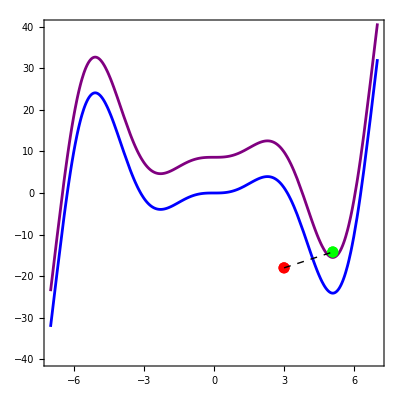
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

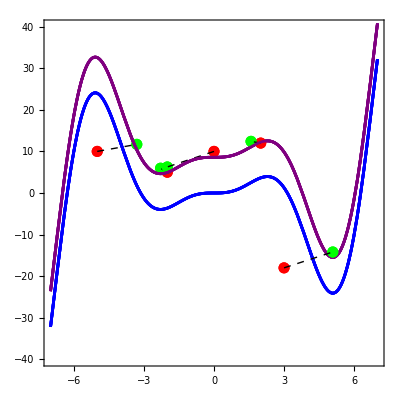

```mathematica
(*Define the norm types for each point*)
normType={3,3, 3, 3, 3, 3};

(*Define the filenames for the CSV files*)
filename={"output3_p4_1_2c_1.csv","output3_p4_1_2c_2.csv","output3_p4_1_2c_3.csv","output3_p4_1_2c_4.csv","output3_p4_1_2c_5.csv"};

(*Call the function*)
plots=plotOptimizedF[f,8.59,m,xMin,xMax,yMin,yMax,normType,filename]

(*Display the plots*)
Show[plots]
```

Produced a score of 4.327 at a = 9.8003333.0

### Analysis

We were able to take a vector of distances computed from before and optimize it such that we continually compute the norm of the distance vector until the distances are 
as small as possible given our method, computing a score based on the norm chosen. This allows for continually shifting the graph of f to minimize the distance between the points and the function overall.

After testing all 3 norms, I found that Norm Infinity performed just a bit better than the other 2. Norm 2 performed noticeably better than Norm 1, producing an  a value only 0.4 below Norm Infinity’s ‘a’.
There were significant changes in the score, going from 10 to 4, too.

This could be due to the way each norm is calculated. 
 - Norm 1 calculates the sum of the absolute differences of their coordinates. It is less sensitive to outliers than the others.
 - Norm 2 calculates the square root of the sum of the squares of differences of their coordinates. It is more sensitive to outliers than  Norm 1.
- Norm Infinity calculates the maximum of the absolute differences of their coordinates. It is even more sensitive to outliers than the others.

Since this example only had 1 outlier at (3, -18), the results were actually in favor of the other norms over norm 1. If this example included more than 5 data points, more of which were outliers, I think norm 1 would perform better.